```mathematica
m=1.;
V[z_]:=3 Tanh[z]^2-1;
```

```mathematica
ℒ=(-1/2 D[η[z], z,z]+V[z] η[z]) m^2
```

1. ((-1+3 Tanh[z]^2) η[z]-η''[z]/2)

```mathematica
{vals,funs}=NDEigensystem[ℒ,η[z],{z,-5,5},6,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}];
```

```mathematica
vals
```

{-9.88901×10^-8,1.49946,2.00008,2.09716,2.36092,2.7571}

```mathematica
funs
```

{InterpolatingFunction[…][z],InterpolatingFunction[…][z],InterpolatingFunction[…][z],InterpolatingFunction[…][z],InterpolatingFunction[…][z],InterpolatingFunction[…][z]}

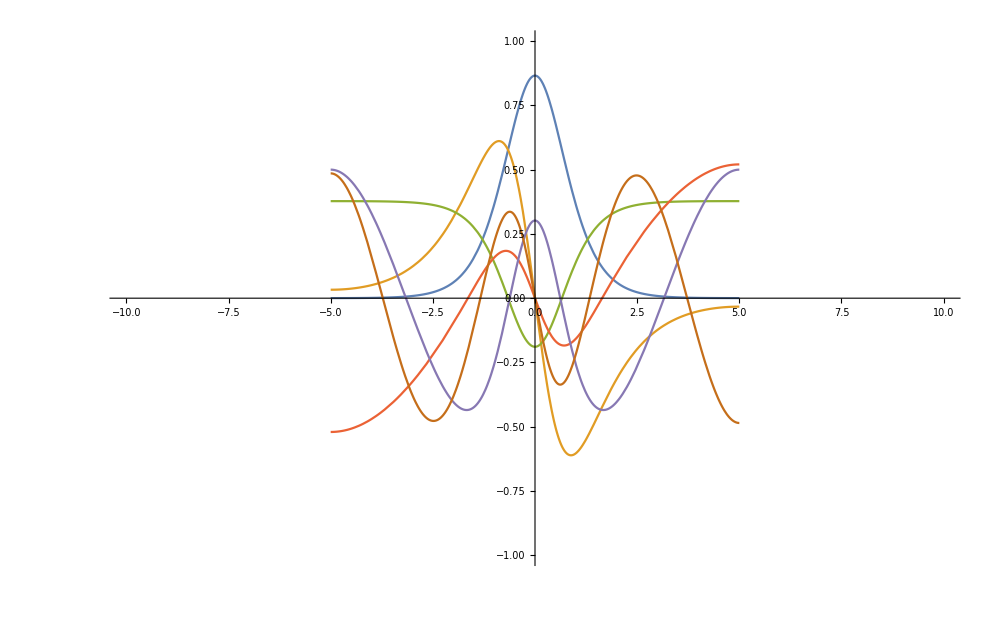

```mathematica
Show[Plot[Evaluate[m*funs],{z,-10,10}],PlotRange->{{-10,10},{-1,1}},AxesOrigin->{0,0},ImageSize->1000]
```